```mathematica
eps=0.5*10^-4;
δ=0.25;
```

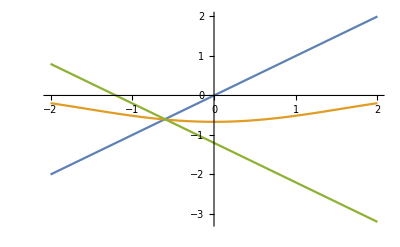

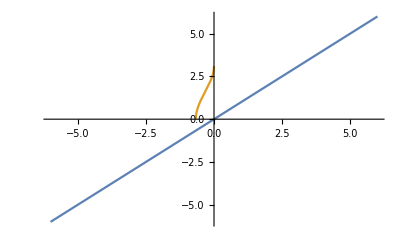

```mathematica
f[x_]:=3*x+Cos[x]+1=0;
x01=-0.6;
Plot[{x,(-Cos[x]-1)/3,-x+2x01},{x,-2,2}]
Plot[{x,ArcCos[-3*x-1]},{x,-6,6}]
```

```mathematica
(*по последнему графику видно, что корней нет => корень только 1 *)
(*поиск корня с начальным приближением 0.6*)
```

```mathematica
ϕ[x_]=((-Cos[x]-1)/3);

(*проверка на условие Липшица*)
d[x_,y_]:=Abs[x-y];
Subscript[d, ϕ][x_,y_]:=Abs[ϕ[x]-ϕ[y]];
Plot3D[Subscript[d, ϕ][x,y]/d[x,y],{x,x01-δ,x01+δ},{y,x01-δ,x01+δ}]
Print["q < 0.9, можно взять q = 0.9"]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

-Graphics3D-

q < 0.9, можно взять q = 0.9

```mathematica
q=0.9;
Print[Abs[ϕ[x01]-x01]," <= ",(1-q)δ, ", q = ", q, " => условия теоремы удовлетворены => ∃! решение x^* на отрезке S"];
```

0.0084452 <= 0.025, q = 0.9 => условия теоремы удовлетворены => ∃! решение x^* на отрезке S

```mathematica
Subscript[x, n]=x01;
Subscript[x, n+1]=ϕ[x01];

While[Abs[Subscript[x, n+1]-Subscript[x, n]]>eps,
	{Subscript[x, n],Subscript[x, n+1]}={Subscript[x, n+1],ϕ[Subscript[x, n+1]]};
Print["x_n=",Subscript[x, n],"   x_(n + 1)=",Subscript[x, n+1],"    Abs = ", Abs[Subscript[x, n+1]-Subscript[x, n]]];
];

Print["x^* = ",Subscript[x, n+1]];
Print["f(x^*) = ", f[Subscript[x, n+1]]];
```

x_n=-0.608445   x_(n + 1)=-0.606846    Abs = 0.0015993

x_n=-0.606846   x_(n + 1)=-0.60715    Abs = 0.000304366

x_n=-0.60715   x_(n + 1)=-0.607092    Abs = 0.0000578705

x_n=-0.607092   x_(n + 1)=-0.607103    Abs = 0.0000110052

x^* = -0.607103

f(x^*) = 0